```mathematica
SetDirectory[NotebookDirectory[]];
points = Import["project\\project\\in.txt", "Table"][[2;;]];
polygon =Import["project\\project\\out.txt", "Table"][[2;;]]
```

{{-1.63423,-0.617773},{-1.54083,0.946829},{1.28229,0.708425},{1.49489,0.377652},{1.49489,0.377652},{0.815421,-0.468176},{-0.32008,-0.58109},{-1.63423,-0.617773}}

```mathematica
ListPlot[points,PlotStyle->Red, PlotRange->All];
```

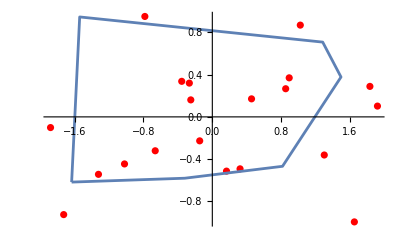

```mathematica
Show[ListPlot[points,PlotStyle->Red], ListLinePlot[polygon], PlotRange->All]
```

```mathematica
points2 = Import["task2\\task2\\in.txt", "Table"][[2;;]]
polygon2 =Import["task2\\task2\\out.txt", "Table"][[2;;]]
```

{{0.322155,-0.492222},{0.455563,0.170841},{-0.250036,0.16102},{1.8307,0.288838},{0.893157,0.369983},{1.91843,0.102253},{0.85217,0.266743},{-0.783653,0.95143},{1.30045,-0.361153},{-0.14663,-0.227033},{0.164728,-0.513837},{-1.72664,-0.925785},{-1.87938,-0.101262},{-0.355414,0.336885},{-1.02008,-0.445801},{-1.32258,-0.544284},{1.02205,0.869363},{-0.663305,-0.321069},{1.65012,-0.994884},{-0.267001,0.320064}}

{{1.65012,-0.994884},{1.91843,0.102253},{1.8307,0.288838},{1.02205,0.869363},{-0.783653,0.95143},{-1.87938,-0.101262},{-1.72664,-0.925785},{1.65012,-0.994884}}

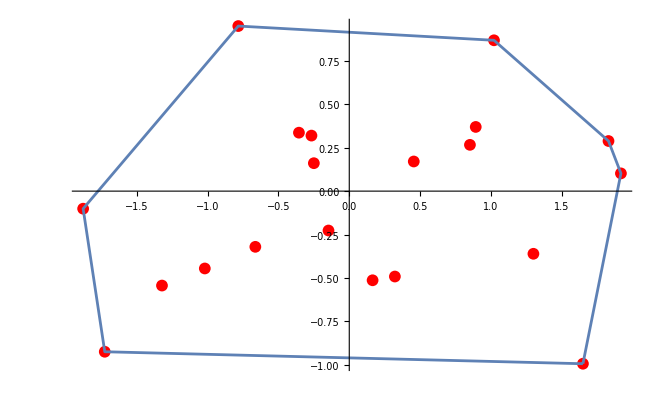

```mathematica
Show[ListPlot[points2,PlotStyle->Red], ListLinePlot[polygon2], PlotRange->All]
```